# Characteristics of Eigen(new)

## 基本的性質

```mathematica
A={{1,2,5},{2,3,6},{9,3,1}}
```

{{1,2,5},{2,3,6},{9,3,1}}

```mathematica
v=Eigenvalues[A]//N
```

{10.5457,-5.80694,0.261275}

```mathematica
u=Eigenvectors[A]//N
```

{{0.730993,0.98891,1.},{-0.572576,-0.551252,1.},{0.856735,-2.81645,1.}}

```mathematica
A.u[[1]]
```

{7.70881,10.4287,10.5457}

```mathematica
v[[1]] u[[1]]
```

{7.70881,10.4287,10.5457}

```mathematica
u[[1]].u[[2]]
```

0.0363118

```mathematica
uT=Transpose[u];
```

```mathematica
uT[[1]].uT[[2]]
```

-1.37443

対称行列の固有ベクトルの転置(ベクトル)は直行する。

一般的に固有値はノルムの大きい固有値順に求まる(ソートされる)。

## 対称行列の固有値・固有ベクトルの性質

1. eigen valuesは行列を並べ替えても保たれるか:
=> 行列の行と列を同じオーダーで入れ替えると保たれる。

2. eigen valuesはzeroのインサートにより保たれるか:
=> 行列に対する同じオーダーでの挿入により保たれる。

3. eigen vectorの要素の絶対値の大きさ順に行列を並べ替えた後のeigen vectorは、大きさの順位を保っているか:
=> 保たれている。

4. mat.Eigenvectors.PCA == matReOrder[mat].Eigenvectors.PCA <= True
    mat.PCA == matReOrder[mat].PCA <= NotTrue

## Program

```mathematica
Get["/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/List_operations.txt"]
```

```mathematica
Get["/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/Matrix_operations.txt"]
```

```mathematica
Get["/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/Chemicalform_operations.txt"]
```

```mathematica
(*Get["/Users/amanokou/gitsrc/MATH_SCRIPT/SCRIPTS/Matrix_operations.txt"]*)
```

## Matrix types (特別な行列のタイプ)

```mathematica
??Eigenvectors
```

RowBox[{"Eigenvectors", "[", StyleBox["m", "TI"], "]"}] 正方行列 StyleBox[RowBox[{"m", " "}], "TI"]の固有ベクトルのリストを与える．
RowBox[{"Eigenvectors", "[", RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["a", "TI"]}], "}"}], "]"}] StyleBox[RowBox[{"a", " "}], "TI"]についての StyleBox[RowBox[{"m", " "}], "TI"]の一般化された固有ベクトルを与える．
RowBox[{"Eigenvectors", "[", RowBox[{StyleBox["m", "TI"], ",", StyleBox["k", "TI"]}], "]"}] StyleBox[RowBox[{"m", " "}], "TI"]の最初のStyleBox[RowBox[{" ", "k", " "}], "TI"]個の固有ベクトルを与える．
RowBox[{"Eigenvectors", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["a", "TI"]}], "}"}], ",", StyleBox["k", "TI"]}], "]"}] 最初の StyleBox[RowBox[{"k", " "}], "TI"]個の一般化された固有ベクトルを与える．

Attributes[Eigenvectors]={Protected}
 
Options[Eigenvectors]={Cubics→False,Method→Automatic,Quartics→False,ZeroTest→Automatic}

Column vector correspond to each vector of original matrix.

Row vector correspond to 1st property of all vector of original matrix.

```mathematica
??IncidenceMatrix
```

RowBox[{"IncidenceMatrix", "[", StyleBox["g", "TI"], "]"}] gives the vertex-edge incidence matrix of the graph StyleBox["g", "TI"].
RowBox[{"IncidenceMatrix", "[", RowBox[{"{", RowBox[{RowBox[{StyleBox["v", "TI"], "→", StyleBox["w", "TI"]}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] uses rules RowBox[{StyleBox["v", "TI"], "→", StyleBox["w", "TI"]}] to specify the graph StyleBox["g", "TI"].

Attributes[IncidenceMatrix]={Protected}

```mathematica
??KirchhoffMatrix (*Laplacian matrix*)
```

RowBox[{"KirchhoffMatrix", "[", StyleBox["g", "TI"], "]"}] gives the Kirchhoff matrix of the graph StyleBox["g", "TI"].
RowBox[{"KirchhoffMatrix", "[", RowBox[{"{", RowBox[{RowBox[{StyleBox["v", "TI"], "→", StyleBox["w", "TI"]}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] uses rules RowBox[{StyleBox["v", "TI"], "→", StyleBox["w", "TI"]}] to specify the graph StyleBox["g", "TI"].

Attributes[KirchhoffMatrix]={Protected,ReadProtected}

Information::nomatch: No symbol matching (*Laplacian found.

Information::nomatch: No symbol matching matrix*) found.

## 密行列

## 密行列

### Eigenvalues

```mathematica
(m=Table[RandomReal[],{6},{6}])//TableForm
```

0.217088 | 0.297605 | 0.535894 | 0.724269 | 0.217514 | 0.791755
0.731076 | 0.83272 | 0.536448 | 0.872905 | 0.457885 | 0.727105
0.416784 | 0.597746 | 0.259568 | 0.780753 | 0.914124 | 0.972288
0.653291 | 0.292778 | 0.793259 | 0.46835 | 0.0257706 | 0.80426
0.103996 | 0.769124 | 0.0173882 | 0.685472 | 0.778817 | 0.965742
0.0870684 | 0.913185 | 0.369686 | 0.409116 | 0.277998 | 0.658388

```mathematica
Eigenvalues[m]
```

{3.30643+0. ⅈ,0.193348+0.459324 ⅈ,0.193348-0.459324 ⅈ,-0.0961402+0.318175 ⅈ,-0.0961402-0.318175 ⅈ,-0.285913+0. ⅈ}

```mathematica
Eigenvalues[2 m]
```

{6.61286+0. ⅈ,0.386695+0.918647 ⅈ,0.386695-0.918647 ⅈ,-0.19228+0.636351 ⅈ,-0.19228-0.636351 ⅈ,-0.571825+0. ⅈ}

```mathematica
ro={2,3,5,1,6,4}
```

{2,3,5,1,6,4}

```mathematica
Eigenvalues[matRowReOrder[m,ro]]
```

{3.27424+0. ⅈ,-0.621385+0. ⅈ,0.353865+0. ⅈ,0.217272+0.278684 ⅈ,0.217272-0.278684 ⅈ,-0.288524+0. ⅈ}

```mathematica
Eigenvalues[matColReOrder[m,ro]]
```

{3.25126,0.807527,-0.51285,0.373404,-0.309637,0.166619}

```mathematica
Eigenvalues[matReOrder[m,ro]]
```

{3.30643+0. ⅈ,0.193348+0.459324 ⅈ,0.193348-0.459324 ⅈ,-0.0961402+0.318175 ⅈ,-0.0961402-0.318175 ⅈ,-0.285913+0. ⅈ}

```mathematica
Eigenvalues[zeroInsert[m,2,3]]
```

{3.30643+0. ⅈ,0.193348+0.459324 ⅈ,0.193348-0.459324 ⅈ,-0.0961402+0.318175 ⅈ,-0.0961402-0.318175 ⅈ,-0.285913+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

### Eigenvectors

```mathematica
ev1=(ev=Eigenvectors[m])[[1]]
```

{0.332613+0. ⅈ,0.504781+0. ⅈ,0.469226+0. ⅈ,0.36225+0. ⅈ,0.401977+0. ⅈ,0.348686+0. ⅈ}

```mathematica
ev2=(ev=Eigenvectors[2 m])[[1]]
```

{0.332613+0. ⅈ,0.504781+0. ⅈ,0.469226+0. ⅈ,0.36225+0. ⅈ,0.401977+0. ⅈ,0.348686+0. ⅈ}

```mathematica
ro=Ordering[Eigenvectors[m][[1]],All,Abs[#1]>Abs[#2]&]
```

{2,3,5,4,6,1}

```mathematica
evro=Eigenvectors[matReOrder[m, ro]][[1]]
```

{-0.504781+0. ⅈ,-0.469226+0. ⅈ,-0.401977+0. ⅈ,-0.36225+0. ⅈ,-0.348686+0. ⅈ,-0.332613+0. ⅈ}

```mathematica
Map[Abs,evro]
```

{0.504781,0.469226,0.401977,0.36225,0.348686,0.332613}

```mathematica
Ordering[evor, All,Abs[#1]>Abs[#2]&]
```

Ordering::normal: Ordering[evor, All, Abs[#1] > Abs[#2] &]で1の位置に原子的ではない式が想定されます．

Ordering[evor,All,Abs[#1]>Abs[#2]&]

## 密行列(Symmetric)

```mathematica
m1={{8,0,1},
{0,1,0},
{1,0,3}
}
```

{{8,0,1},{0,1,0},{1,0,3}}

### Reorder

```mathematica
m1r=matReOrder[m1,{2,1,3}]
```

{{1,0,0},{0,8,1},{0,1,3}}

```mathematica
Eigenvalues[m1]//N
```

{8.19258,2.80742,1.}

```mathematica
Eigenvalues[m1r]//N
```

{8.19258,2.80742,1.}

```mathematica
(eigm1=Eigenvectors[m1])//N//TableForm
```

5.19258 | 0. | 1.
-0.192582 | 0. | 1.
0. | 1. | 0.

```mathematica
Eigenvectors[m1r]//N//TableForm
```

0. | 5.19258 | 1.
0. | -0.192582 | 1.
1. | 0. | 0.

```mathematica
eigm1[[1]].eigm1[[2]]
```

1+1/4 (5-√29) (5+√29)

```mathematica
eigm1T=Transpose[eigm1];
```

```mathematica
eigm1T[[1]].eigm1T[[2]]
```

0

```mathematica
Map[Norm,eigm1]//N
```

{5.288,1.01838,1.}

```mathematica
Map[Norm,eigm1//Transpose]//N
```

{5.19615,1.,1.41421}

### PCA

```mathematica
PrincipalComponents[m1]//N
```

{{5.01781,0.209219,0.},{-3.00666,1.47724,0.},{-2.01116,-1.68646,0.}}

```mathematica
PrincipalComponents[m1r]//N
```

{{3.00666,1.47724,0.},{-5.01781,0.209219,0.},{2.01116,-1.68646,0.}}

```mathematica
PrincipalComponents[m1]//Eigenvectors//N
```

{{-9.68205,8.68205,1.},{0.0665508,-1.06655,1.},{0.,0.,1.}}

```mathematica
PrincipalComponents[m1r]//Eigenvectors//N
```

{{-0.0212353-0.631712 ⅈ,-0.978765+0.631712 ⅈ,1.},{-0.0212353+0.631712 ⅈ,-0.978765-0.631712 ⅈ,1.},{0.,0.,1.}}

```mathematica
PrincipalComponents[m1//Eigenvectors]//N
```

{{3.55729,0.000491144,0.},{-1.78048,0.713385,0.},{-1.77681,-0.713876,0.}}

```mathematica
PrincipalComponents[m1r//Eigenvectors]//N
```

{{3.55729,0.000491144,0.},{-1.78048,0.713385,0.},{-1.77681,-0.713876,0.}}

```mathematica
{5.0178132378072995,0.20921886317440697,0.}//Norm
```

5.02217

```mathematica
{3.557288822224498,0.0004911436277977636,0.}//Norm
```

3.55729

## 密行列(対角ゼロ)

### Eigenvectors

```mathematica
(mz=(m=Table[RandomReal[],{6},{6}])//zeroTr)//TableForm
```

0 | 0.34184 | 0.829376 | 0.0617657 | 0.447816 | 0.555238
0.940682 | 0 | 0.239217 | 0.38123 | 0.548477 | 0.0686853
0.0856401 | 0.0954907 | 0 | 0.911451 | 0.766821 | 0.649122
0.13786 | 0.88611 | 0.930102 | 0 | 0.514163 | 0.821613
0.796154 | 0.769006 | 0.763072 | 0.0650143 | 0 | 0.411937
0.547239 | 0.402326 | 0.389279 | 0.799408 | 0.269009 | 0

```mathematica
m//MatrixForm
```

(0.949453 | 0.34184 | 0.829376 | 0.0617657 | 0.447816 | 0.555238
0.940682 | 0.849544 | 0.239217 | 0.38123 | 0.548477 | 0.0686853
0.0856401 | 0.0954907 | 0.87718 | 0.911451 | 0.766821 | 0.649122
0.13786 | 0.88611 | 0.930102 | 0.0712852 | 0.514163 | 0.821613
0.796154 | 0.769006 | 0.763072 | 0.0650143 | 0.188714 | 0.411937
0.547239 | 0.402326 | 0.389279 | 0.799408 | 0.269009 | 0.302415)

対角あり

```mathematica
ev1=(ev=Eigenvectors[m])[[1]]
```

{-0.416916+0. ⅈ,-0.397103+0. ⅈ,-0.44562+0. ⅈ,-0.432399+0. ⅈ,-0.392728+0. ⅈ,-0.358758+0. ⅈ}

```mathematica
ro=Ordering[Eigenvectors[m][[1]],All,Abs[#1]>Abs[#2]&]
```

{3,4,1,2,5,6}

```mathematica
evro=Eigenvectors[matReOrder[m, ro]][[1]]
```

{-0.44562+0. ⅈ,-0.432399+0. ⅈ,-0.416916+0. ⅈ,-0.397103+0. ⅈ,-0.392728+0. ⅈ,-0.358758+0. ⅈ}

```mathematica
Map[Abs,evro]
```

{0.44562,0.432399,0.416916,0.397103,0.392728,0.358758}

```mathematica
Ordering[evro, All,Abs[#1]>Abs[#2]&]
```

{1,2,3,4,5,6}

対角ゼロ

```mathematica
ev1=(ev=Eigenvectors[mz])[[1]]
```

{-0.352761+0. ⅈ,-0.342587+0. ⅈ,-0.425736+0. ⅈ,-0.50059+0. ⅈ,-0.414586+0. ⅈ,-0.393027+0. ⅈ}

```mathematica
ro=Ordering[Eigenvectors[mz][[1]],All,Abs[#1]>Abs[#2]&]
```

{4,3,5,6,1,2}

```mathematica
evro=Eigenvectors[matReOrder[mz, ro]][[1]]
```

{0.50059+0. ⅈ,0.425736+0. ⅈ,0.414586+0. ⅈ,0.393027+0. ⅈ,0.352761+0. ⅈ,0.342587+0. ⅈ}

```mathematica
Map[Abs,evro]
```

{0.50059,0.425736,0.414586,0.393027,0.352761,0.342587}

```mathematica
Ordering[evro, All,Abs[#1]>Abs[#2]&]
```

{1,2,3,4,5,6}

## Diagonal+link

```mathematica
m1={{1,0,0},{0,1,0},{0,0,1}}
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
(l1=Table[{i,{{1,i,i},{i,1,i},{i,i,1}}//Eigenvalues},{i,0,2,2/10}])//TableForm
```

0 | 1
1
1
1/5 | 7/5
4/5
4/5
2/5 | 9/5
3/5
3/5
3/5 | 11/5
2/5
2/5
4/5 | 13/5
1/5
1/5
1 | 3
0
0
6/5 | 17/5
-1/5
-1/5
7/5 | 19/5
-2/5
-2/5
8/5 | 21/5
-3/5
-3/5
9/5 | 23/5
-4/5
-4/5
2 | 5
-1
-1

```mathematica
Table[{l1[[i,1]],l1[[i,2,1]]},{i,10}]
```

{{0,1},{1/5,7/5},{2/5,9/5},{3/5,11/5},{4/5,13/5},{1,3},{6/5,17/5},{7/5,19/5},{8/5,21/5},{9/5,23/5}}

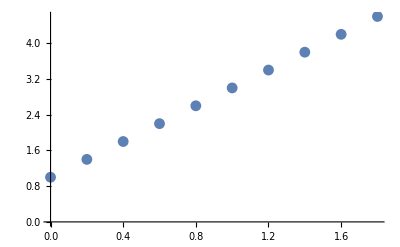

```mathematica
ListPlot[Table[{l1[[i,1]],l1[[i,2,1]]},{i,10}]]
```

```mathematica
(l2=Table[{i,{{1,i,0},{i,1,i},{0,i,1}}//Eigenvalues},{i,0,2,2/10}])//TableForm
```

0 | 1
1
1
1/5 | 1/5 (5+√2)
1
1/5 (5-√2)
2/5 | 1/5 (5+2 √2)
1
1/5 (5-2 √2)
3/5 | 1/5 (5+3 √2)
1
1/5 (5-3 √2)
4/5 | 1/5 (5+4 √2)
1
1/5 (5-4 √2)
1 | 1+√2
1
1-√2
6/5 | 1/5 (5+6 √2)
1
1/5 (5-6 √2)
7/5 | 1/5 (5+7 √2)
1
1/5 (5-7 √2)
8/5 | 1/5 (5+8 √2)
1/5 (5-8 √2)
1
9/5 | 1/5 (5+9 √2)
1/5 (5-9 √2)
1
2 | 1+2 √2
1-2 √2
1

```mathematica
Table[{l2[[i,1]],l2[[i,2,1]]},{i,10}]
```

{{0,1},{1/5,1/5 (5+√2)},{2/5,1/5 (5+2 √2)},{3/5,1/5 (5+3 √2)},{4/5,1/5 (5+4 √2)},{1,1+√2},{6/5,1/5 (5+6 √2)},{7/5,1/5 (5+7 √2)},{8/5,1/5 (5+8 √2)},{9/5,1/5 (5+9 √2)}}

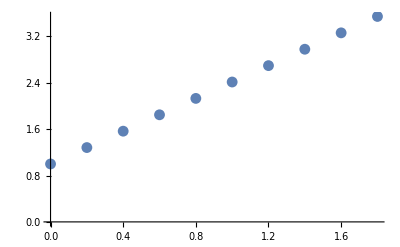

```mathematica
ListPlot[Table[{l2[[i,1]],l2[[i,2,1]]},{i,10}]]
```

```mathematica
(l3=Table[{i,{{1,i,0},{i,1,0},{0,0,1}}//Eigenvalues},{i,0,2,2/10}])//TableForm
```

0 | 1
1
1
1/5 | 6/5
1
4/5
2/5 | 7/5
1
3/5
3/5 | 8/5
1
2/5
4/5 | 9/5
1
1/5
1 | 2
1
0
6/5 | 11/5
1
-1/5
7/5 | 12/5
1
-2/5
8/5 | 13/5
1
-3/5
9/5 | 14/5
1
-4/5
2 | 3
-1
1

```mathematica
Table[{l3[[i,1]],l3[[i,2,1]]},{i,10}]
```

{{0,1},{1/5,6/5},{2/5,7/5},{3/5,8/5},{4/5,9/5},{1,2},{6/5,11/5},{7/5,12/5},{8/5,13/5},{9/5,14/5}}

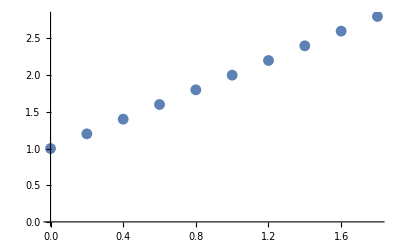

```mathematica
ListPlot[Table[{l3[[i,1]],l3[[i,2,1]]},{i,10}]]
```

```mathematica
Table[{i,{{1,i,i},{i,1,i},{i,i,1}}//Eigenvectors},{i,0,2,2/10}]//TableForm
```

0 | 0 | 0 | 1
0 | 1 | 0
1 | 0 | 0
1/5 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0
2/5 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0
3/5 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0
4/5 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0
1 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0
6/5 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0
7/5 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0
8/5 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0
9/5 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0
2 | 1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0

```mathematica
Table[{i,{{1,i,i,i},{i,1,i,i},{i,i,1,i},{i,i,i,1}}//Eigenvalues},{i,0,2,1/5}]//TableForm
```

0 | 1
1
1
1
1/5 | 8/5
4/5
4/5
4/5
2/5 | 11/5
3/5
3/5
3/5
3/5 | 14/5
2/5
2/5
2/5
4/5 | 17/5
1/5
1/5
1/5
1 | 4
0
0
0
6/5 | 23/5
-1/5
-1/5
-1/5
7/5 | 26/5
-2/5
-2/5
-2/5
8/5 | 29/5
-3/5
-3/5
-3/5
9/5 | 32/5
-4/5
-4/5
-4/5
2 | 7
-1
-1
-1

```mathematica
m={{1,0,0},{0,2,0},{0,0,3}}
```

{{1,0,0},{0,2,0},{0,0,3}}

```mathematica
Eigenvalues[m]
```

{3,2,1}

```mathematica
Eigenvectors[m]
```

{{0,0,1},{0,1,0},{1,0,0}}

```mathematica
Table[{i,e=Eigenvalues[{{1,0,0},{0,2,i},{0,i,3}}],e//Tr},{i,0,2,0.2}]//TableForm
```

0. | 3.
2.
1. | 6.
0.2 | 3.03852
1.96148
1. | 6.
0.4 | 3.14031
1.85969
1. | 6.
0.6 | 3.28102
1.71898
1. | 6.
0.8 | 3.4434
1.5566
1. | 6.
1. | 3.61803
1.38197
1. | 6.
1.2 | 3.8
1.2
1. | 6.
1.4 | 3.98661
1.01339
1. | 6.
1.6 | 4.17631
1.
0.823695 | 6.
1.8 | 4.36815
1.
0.631846 | 6.
2. | 4.56155
1.
0.438447 | 6.

```mathematica
3.0385164807134504-1.9614835192865496
```

1.07703

## Symmetric matrix

### Eigenvalues

```mathematica
(mz=(m=createRandomSymMat[10])//zeroTr)//TableForm
```

0 | 0.248134 | 0.0956967 | 0.240373 | 0.677053 | 0.656126 | 0.737405 | 0.82831 | 0.739874 | 0.766126
0.248134 | 0 | 0.574316 | 0.455944 | 0.204624 | 0.467184 | 0.945298 | 0.485438 | 0.122277 | 0.209314
0.0956967 | 0.574316 | 0 | 0.0674961 | 0.82164 | 0.279233 | 0.757785 | 0.579644 | 0.188105 | 0.040455
0.240373 | 0.455944 | 0.0674961 | 0 | 0.2444 | 0.681082 | 0.877396 | 0.0436435 | 0.531625 | 0.0318154
0.677053 | 0.204624 | 0.82164 | 0.2444 | 0 | 0.0860069 | 0.0440143 | 0.758082 | 0.831012 | 0.282224
0.656126 | 0.467184 | 0.279233 | 0.681082 | 0.0860069 | 0 | 0.809091 | 0.776618 | 0.632042 | 0.000327158
0.737405 | 0.945298 | 0.757785 | 0.877396 | 0.0440143 | 0.809091 | 0 | 0.350299 | 0.581782 | 0.292032
0.82831 | 0.485438 | 0.579644 | 0.0436435 | 0.758082 | 0.776618 | 0.350299 | 0 | 0.940422 | 0.128361
0.739874 | 0.122277 | 0.188105 | 0.531625 | 0.831012 | 0.632042 | 0.581782 | 0.940422 | 0 | 0.782158
0.766126 | 0.209314 | 0.040455 | 0.0318154 | 0.282224 | 0.000327158 | 0.292032 | 0.128361 | 0.782158 | 0

```mathematica
m//TableForm
```

0.181737 | 0.248134 | 0.0956967 | 0.240373 | 0.677053 | 0.656126 | 0.737405 | 0.82831 | 0.739874 | 0.766126
0.248134 | 0.298499 | 0.574316 | 0.455944 | 0.204624 | 0.467184 | 0.945298 | 0.485438 | 0.122277 | 0.209314
0.0956967 | 0.574316 | 0.967562 | 0.0674961 | 0.82164 | 0.279233 | 0.757785 | 0.579644 | 0.188105 | 0.040455
0.240373 | 0.455944 | 0.0674961 | 0.946202 | 0.2444 | 0.681082 | 0.877396 | 0.0436435 | 0.531625 | 0.0318154
0.677053 | 0.204624 | 0.82164 | 0.2444 | 0.460362 | 0.0860069 | 0.0440143 | 0.758082 | 0.831012 | 0.282224
0.656126 | 0.467184 | 0.279233 | 0.681082 | 0.0860069 | 0.504051 | 0.809091 | 0.776618 | 0.632042 | 0.000327158
0.737405 | 0.945298 | 0.757785 | 0.877396 | 0.0440143 | 0.809091 | 0.2495 | 0.350299 | 0.581782 | 0.292032
0.82831 | 0.485438 | 0.579644 | 0.0436435 | 0.758082 | 0.776618 | 0.350299 | 0.412108 | 0.940422 | 0.128361
0.739874 | 0.122277 | 0.188105 | 0.531625 | 0.831012 | 0.632042 | 0.581782 | 0.940422 | 0.507026 | 0.782158
0.766126 | 0.209314 | 0.040455 | 0.0318154 | 0.282224 | 0.000327158 | 0.292032 | 0.128361 | 0.782158 | 0.888375

```mathematica
v=Eigenvalues[m]
```

{4.83612,1.57894,1.31066,-1.29155,-0.786573,0.675378,-0.622519,-0.43626,0.400201,-0.248974}

```mathematica
or=Ordering[v,All,Abs[#1]>Abs[#2]&]
```

{1,2,3,4,5,6,7,8,9,10}

## Intensity Matrix

```mathematica
eigenIntensity[m]//N//MatrixForm
```

(-1.30295+0. ⅈ | -1.24103+0. ⅈ | -1.39265+0. ⅈ | -1.35134+0. ⅈ | -1.22736+0. ⅈ | -1.12119+0. ⅈ
0.196629+0. ⅈ | -0.292503+0. ⅈ | -0.336182+0. ⅈ | 0.634345+0. ⅈ | 0.379987+0. ⅈ | -0.371003+0. ⅈ
-0.246021+0.206326 ⅈ | 0.406197+0.286391 ⅈ | -0.260856-0.346898 ⅈ | 0.14452-0.158302 ⅈ | 0.0369093+0.141772 ⅈ | 0.0626156-0.0697663 ⅈ
-0.246021-0.206326 ⅈ | 0.406197-0.286391 ⅈ | -0.260856+0.346898 ⅈ | 0.14452+0.158302 ⅈ | 0.0369093-0.141772 ⅈ | 0.0626156+0.0697663 ⅈ
-0.0170972+0. ⅈ | -0.0542011+0. ⅈ | -0.171963+0. ⅈ | -0.0705667+0. ⅈ | 0.255037+0. ⅈ | 0.13231+0. ⅈ
0.0246427+0. ⅈ | -0.00073231+0. ⅈ | -0.0813538+0. ⅈ | 0.0102398+0. ⅈ | -0.0262251+0. ⅈ | 0.106004+0. ⅈ)

## 疎行列

## Memo

```mathematica
B
```

{{ⅈ,0,0},{0,ⅈ,0},{0,0,ⅈ}}

```mathematica
Bl={{I,I,0},{0,I,0},{0,0,I}}
```

{{ⅈ,ⅈ,0},{0,ⅈ,0},{0,0,ⅈ}}

```mathematica
Bc={{Normalize[I+1],0,0},{0,I,0},{0,0,I}}
```

{{(1+ⅈ)/(√2),0,0},{0,ⅈ,0},{0,0,ⅈ}}

```mathematica
Bcl={{Normalize[I+1],I,0},{0,I,0},{0,0,I}}
```

{{(1+ⅈ)/(√2),ⅈ,0},{0,ⅈ,0},{0,0,ⅈ}}

```mathematica
Eigensystem[B]
```

{{ⅈ,ⅈ,ⅈ},{{0,0,1},{0,1,0},{1,0,0}}}

```mathematica
Eigensystem[Bl]
```

{{ⅈ,ⅈ,ⅈ},{{0,0,1},{1,0,0},{0,0,0}}}

```mathematica
Eigensystem[Bc]
```

{{ⅈ,ⅈ,(1+ⅈ)/(√2)},{{0,0,1},{0,1,0},{1,0,0}}}

```mathematica
Eigensystem[Bcl]
```

{{ⅈ,ⅈ,(1+ⅈ)/(√2)},{{0,0,1},{-(1+ⅈ)/((-1-ⅈ)+√2),1,0},{1,0,0}}}

```mathematica
Norm[{-(1-ⅈ)/((-1-ⅈ)+√2),1,0}]//N
```

1.64533

```mathematica
EuclideanDistance[Normalize[2I+1],Normalize[I+2]]//N
```

0.632456

```mathematica
EuclideanDistance[Normalize[3I+1],Normalize[I+3]]//N
```

0.894427